```mathematica
newton[f_, x0_, eps_: 0.001]:=Module[{xn, i=0, , xp = x0},
xn = xp - f[xp]/f'[xp];
While[Abs[xn-xp]> eps, 
xp = xn;
xn = xp - f[xp]/f'[xp];
i++;];
Return[xn];
]
```

```mathematica
(*метод ньютона*)
```

```mathematica
f[x_]:=x^3 - 1
```

```mathematica
newton[f, 3+2.ⅈ]
```

1.-1.96754×10^-12 ⅈ

```mathematica
z = 3+ⅈ
```

3+ⅈ

```mathematica
x = Re[z]
```

3

```mathematica
y = Im[z]
```

1

```mathematica
Abs[z]
```

√10

```mathematica
Arg[z]
```

ArcTan[1/3]

```mathematica
Conjugate[z]
```

3-ⅈ

```mathematica
arr = Table[Sin[x*y], {x, -2, 2, 0.01}, {y, -2, 2, 0.01}];
```

```mathematica
Dimensions[arr]
```

{401,401}

```mathematica
ListContourPlot[arr, PlotLegends->Automatic, ColorFunction->"Rainbow"]
```

-Graphics-

```mathematica
ListPlot3D[arr]
```

-Graphics3D-

```mathematica
arr2 = Table[Sin[x+y*ⅈ], {x, -2, 2, 0.01}, {y, -2, 2, 0.01}];
```

```mathematica
Dimensions[arr2]
```

{401,401}

```mathematica
arr3 = Table[newton[f, Sin[x+y*ⅈ]], {x, -2, 2, 0.01}, {y, -2, 2, 0.01}];
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

```mathematica
sol = x/. Solve[f[x]==0, x] //N
```

{1.,-0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ}

```mathematica
root = -0.5000000000000001-0.8660254037844386 ⅈ
```

-0.5-0.866025 ⅈ

```mathematica
Abs[sol - root]
```

{1.73205,0.,1.73205}

```mathematica
Ordering[%5][[1]]
```

2

```mathematica
ClearAll[arr, arr2, f]
```

```mathematica
arr = Table[{x, y, Sin[x*y]}, {x, 0, 2π,  0.05}, {y, 0, π, 0.05}]
```

{{{0.,0.,0.},{0.,0.05,0.},{0.,0.1,0.},{0.,0.15,0.},{0.,0.2,0.},{0.,0.25,0.},51,{0.,2.85,0.},{0.,2.9,0.},{0.,2.95,0.},{0.,3.,0.},{0.,3.05,0.},{0.,3.1,0.}},124,{1}}
 |  |  |  |

```mathematica
arr = Partition[Flatten[arr], 3]
```

{{0.,0.,0.},{0.,0.05,0.},{0.,0.1,0.},{0.,0.15,0.},{0.,0.2,0.},7929,{6.25,2.95,-0.400494},{6.25,3.,-0.0993915},{6.25,3.05,0.211338},{6.25,3.1,0.501597}}
 |  |  |  |

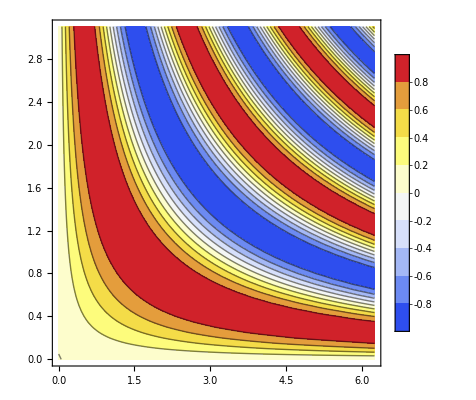

```mathematica
ListContourPlot[arr, ColorFunction->"TemperatureMap", PlotLegends->Automatic]
```

```mathematica
newtonI[f_, x0_, eps_: 0.001]:=Module[{xn, i=0, , xp = x0},
xn = xp - f[xp]/f'[xp];
While[Abs[xn-xp]> eps, 
xp = xn;
xn = xp - f[xp]/f'[xp];
i++;];
Return[i];
]
```

```mathematica
Clear[arr, f]
```

```mathematica
f[x_] := x^3 -1
```

```mathematica
arr = Table[newtonI[f,  x+y*ⅈ], {x, -2, 2, 0.03}, {y, -2, 2, 0.03}]
```

{1}
 |  |  |  |

```mathematica
arr[[1]]
```

{5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,8,8,9,10,14,12,10,8,7,8,11,15,9,8,8,8,8,9,12,13,9,7,7,9,10,17,12,9,8,8,7,7,7,7,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}

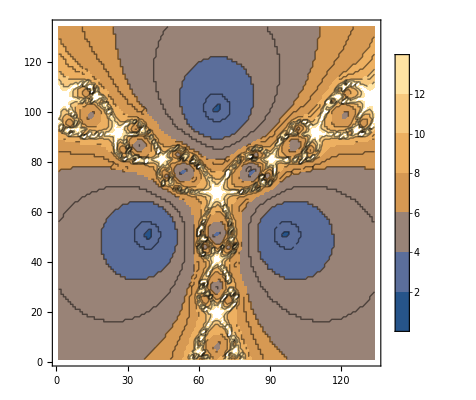

```mathematica
ListContourPlot[arr, PlotLegends->Automatic]
```

```mathematica
newton[f_, x0_, eps_: 0.001]:=Module[{xn, i=0, , xp = x0},
xn = xp - f[xp]/f'[xp];
While[Abs[xn-xp]> eps, 
xp = xn;
xn = xp - f[xp]/f'[xp];
i++;];
Return[xn];
]
```

```mathematica
f1[x_]:= x^5 - 1
```

```mathematica
sol1 = x/. Solve[x^5 - 1 == 0, x] // N
```

{1.,-0.809017-0.587785 ⅈ,0.309017+0.951057 ⅈ,0.309017-0.951057 ⅈ,-0.809017+0.587785 ⅈ}

```mathematica
{1.,-0.8090169943749475-0.5877852522924731 ⅈ,0.30901699437494745+0.9510565162951535 ⅈ,0.30901699437494734-0.9510565162951536 ⅈ,-0.8090169943749473+0.5877852522924732 ⅈ}
```

{1.,-0.809017-0.587785 ⅈ,0.309017+0.951057 ⅈ,0.309017-0.951057 ⅈ,-0.809017+0.587785 ⅈ}

```mathematica
num[f_, x_, y_]:=(
a = (x+y*ⅈ);
sol1 = z/. Solve[z^5 - 1 == 0, z] // N;
root1 = newton[f,a];

Return[Ordering[Abs[sol1 - root1]][[1]]];
)
```

```mathematica
arr1 = Table[newton[f1,  x+y*ⅈ], {x, -2, 2, 0.03}, {y, -2, 2, 0.03}]
```

{{-0.809017-0.587785 ⅈ,-0.809017-0.587785 ⅈ,-0.809017-0.587785 ⅈ,128,-0.809017+0.587785 ⅈ,-0.809017+0.587785 ⅈ,-0.809017+0.587785 ⅈ},132,{1}}
 |  |  |  |

```mathematica
arr2 = Table[num[f1, x, y],{x, -2, 2, 0.03}, {y, -2, 2, 0.03}]
```

{{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,3,4,4,4,1,1,2,3,3,3,2,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5},133}
 |  |  |  |

```mathematica
ListContourPlot[arr2, PlotLegends->Automatic]
```

-Graphics-